```mathematica
Definiendo la función de onda en dos regiones
```

```mathematica
α=Sqrt[2V0 ϵ];
β=Sqrt[2V0(1- ϵ)];
```

```mathematica
constantes={ca,cb,cc,cd};
yamerito=Solve[(matriz/.ϵ->bingo/.k->prueba).constantes=={0,0,0,0},{ca,cb,cc,cd}];
constb=cb/.yamerito[[1,1]];
constc=cc/.yamerito[[1,2]];
constd=cd/.yamerito[[1,3]];
```

```mathematica
phi1[x_]:=ca*Exp[I*α*x]+constb*Exp[-I*α*x];
phi2[x_]:=constc*Exp[β*x]+constd*Exp[-β*x];
```

```mathematica
consta1=Re[Integrate[Conjugate[(phi1[x]/.ϵ->bingo/.ca->1)](phi1[x]/.ϵ->bingo/.ca->1),{x,0,a}]];
consta2=Re[Integrate[Conjugate[(phi2[x]/.ϵ->bingo/.ca->1)](phi2[x]/.ϵ->bingo/.ca->1),{x,-b,0}]];
cafinal=Sqrt[1/(consta1+consta2)];
```

```mathematica
funcion1[x_]=Simplify[ExpToTrig[Conjugate[phi1[x]]phi1[x]/.ϵ->bingo/.ca->cafinal]];
funcion2[x_]=Simplify[ExpToTrig[Conjugate[phi2[x]]phi2[x]/.ϵ->bingo/.ca->cafinal]];
```

0.19638 (1. Cosh[1.7523 x]+(0.760418+0.191996 ⅈ) Sinh[1.7523 x]) (1. Cosh[1.7523 Conjugate[x]]+(0.760418-0.191996 ⅈ) Sinh[1.7523 Conjugate[x]])

```mathematica
Clear[funcion1]
```

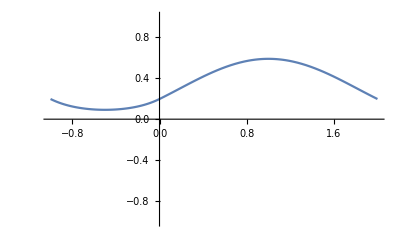

```mathematica
g1=Plot[funcion1[x],{x,0,a},PlotRange->{{-b,a},{-1,1}}];
g2=Plot[funcion2[x],{x,-b,0},PlotRange->{{-b,a},{-1,1}}];
Show[g1,g2]
```